```mathematica
AppendTo[$Path, NotebookDirectory[]];
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
Get["CubeAnimate.wl"]
Get["CubeSolver.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

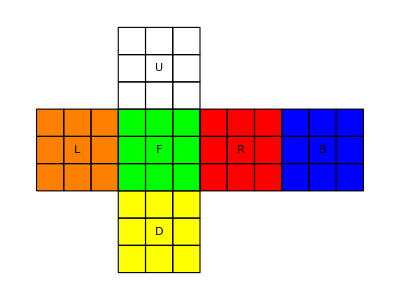

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
Dynamic[GetSolutionMoves[]]
```

-Graphics3D-

### Controlli

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];],
Button["Reset moves string",ResetSolutionMoves[];],
Button["Reset ViewPoint",vp = {1.1,-2.9,1.2};],
Button["Solve",
ResetSolutionMoves[];
SolveCube[];
SetResolutionMoves[solutionMoves];]
]
```

{Load solved,Load start,Reset moves string,Reset ViewPoint,Solve}

```mathematica
List[
Button["Reset",Print["Reset"];],
Button["Prev",
Print["Prev"];
RubikPrev[fps];
DelOut[];
,Enabled->Dynamic[HasPrevMove[]]],
Button["Next", 
Print["Next"];
RubikNext[fps];
DelOut[];
,Enabled->Dynamic[HasNextMove[]]],
"Animation Rate: ", 
fps = 1.5;
Slider[Dynamic[fps], {0.1, 2, 0.1}],
Dynamic[fps]
]
```

{Reset,Prev,Next,Animation Rate: ,,}

```mathematica
DelOut[] := Module[{},
SelectionMove[EvaluationCell[],Next,Cell];
NotebookDelete[];
];
```